## Init, Start

```mathematica
<<MultiAgent`
<<MultiAgent`
```

```mathematica
?initMultiAgentExchange
initMultiAgentExchange[]
```

Function for initialising Multi Agent system (Mono/Multi)

{Days→5,NumberOfProducts→5,AgentsAmount→10,StartMoney→10,ProdFuncInd→1,SessionsInDay→2,FirstPrice→{1,2},FromFile→DefaultTestFile,SystemType→Mono}

```mathematica
?runExchange
agentGoods /@ agentsNums;
runExchange[]
productsNames
hAgentsLastDay
```

main function that runs MAExchange

{Money,Labor,Water,Energy,Ferrum}

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

## Input Params

```mathematica
?printAgentParams
printAgentParams/@agentsNums;
```

prints all agent parameters: id, prod/cons, norm, prodfunc, etc.

***** [1] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {0.00,0.00,0.00,0.00,2.01}

Daily regen: {0.00,0.00,0.00,2.93,0.08}

Start store: {13.87,0.00,0.00,4.15,9.42}

Consume norm: 0.58

Lambda coef: 0.28

***** [2] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {2.17,0.00,0.00,0.00,0.00}

Daily regen: {2.63,2.15,0.00,2.85,1.59}

Start store: {12.03,4.65,0.00,0.00,4.73}

Consume norm: 0.86

Lambda coef: 0.42

***** [3] Agent Parameters *****

Produces good: 1, Money

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {0.00,1.14,0.00,0.00,0.00}

Daily regen: {0.15,0.00,0.04,0.00,1.28}

Start store: {19.67,2.30,0.00,0.00,15.67}

Consume norm: 0.65

Lambda coef: 0.83

***** [4] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.00,1.19,0.00,0.00}

Daily regen: {0.07,0.27,0.16,1.53,0.00}

Start store: {7.02,4.84,7.90,0.00,0.00}

Consume norm: 0.50

Lambda coef: 0.55

***** [5] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.95,0.00,0.00,0.00}

Daily regen: {1.24,1.84,0.89,2.71,1.94}

Start store: {6.69,15.05,16.46,10.88,0.00}

Consume norm: 0.70

Lambda coef: 0.84

***** [6] Agent Parameters *****

Produces good: 3, Water

Consumed good: 4, Energy

Production function: 1

Func coefs : {0.00,0.00,0.00,1.82,0.00}

Daily regen: {0.40,0.00,0.12,0.05,0.00}

Start store: {6.37,0.00,10.28,13.96,0.00}

Consume norm: 0.41

Lambda coef: 0.49

***** [7] Agent Parameters *****

Produces good: 3, Water

Consumed good: 1, Money

Production function: 1

Func coefs : {0.00,0.73,0.00,0.00,0.00}

Daily regen: {2.72,0.00,2.71,0.00,0.00}

Start store: {18.30,13.99,7.56,0.00,0.00}

Consume norm: 0.25

Lambda coef: 0.62

***** [8] Agent Parameters *****

Produces good: 2, Labor

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.00,0.89,0.00,0.00}

Daily regen: {0.00,2.23,0.58,0.98,0.07}

Start store: {7.06,19.71,14.62,0.00,0.00}

Consume norm: 0.50

Lambda coef: 0.57

***** [9] Agent Parameters *****

Produces good: 5, Ferrum

Consumed good: 2, Labor

Production function: 1

Func coefs : {0.00,0.00,1.78,0.00,0.00}

Daily regen: {1.39,1.58,0.00,0.89,0.87}

Start store: {8.94,0.22,9.36,0.00,3.78}

Consume norm: 0.50

Lambda coef: 0.78

***** [10] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.70,0.00,0.00,0.00}

Daily regen: {0.00,0.61,2.03,0.00,0.75}

Start store: {19.86,0.33,15.93,3.65,0.00}

Consume norm: 0.85

Lambda coef: 0.27

```mathematica
<<MultiAgent`
```

```mathematica
MAEVisAgentsHistogram[Automatic]
```

## Agents

[an]: Shows how (an)-agent main curency is changing

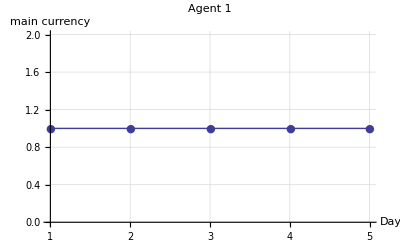
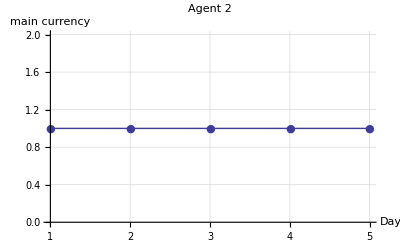
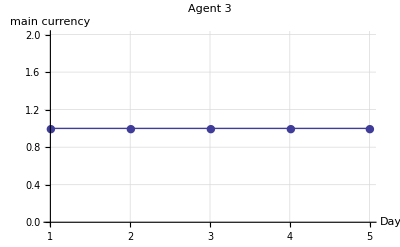
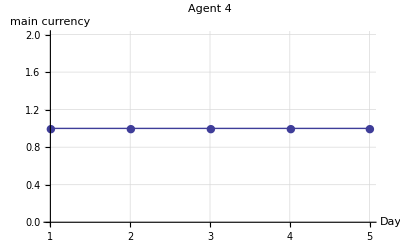
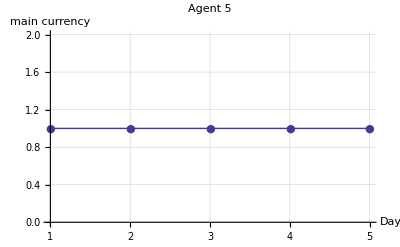
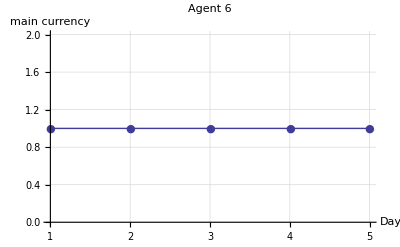
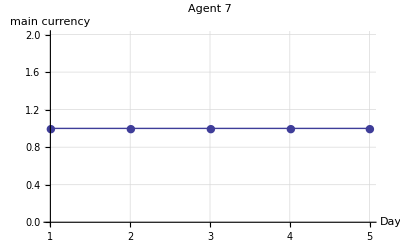
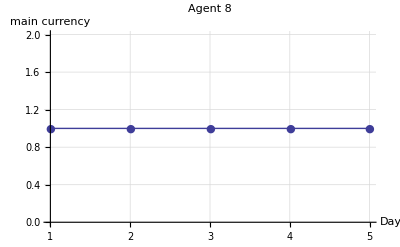

[an]: Shows all production of (an)-agent

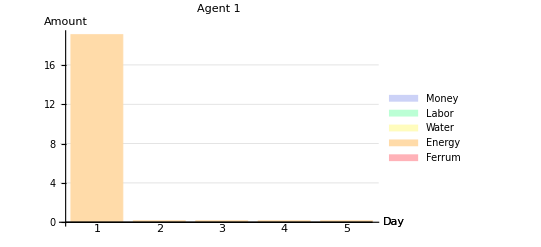
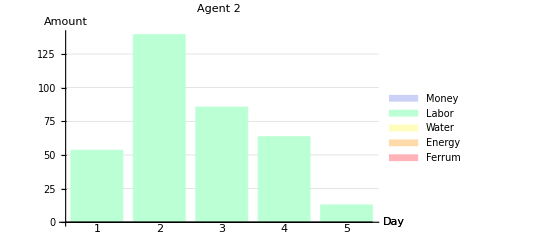
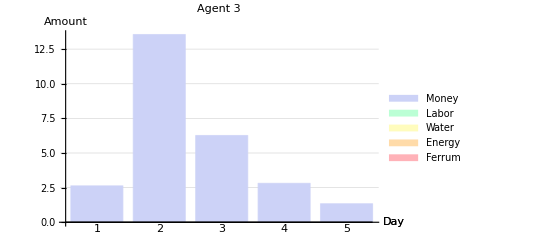
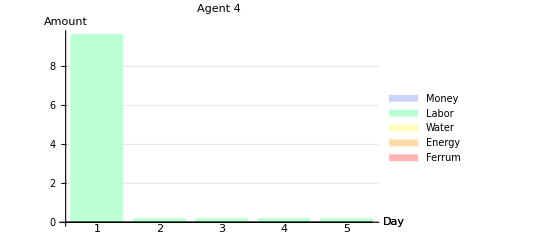
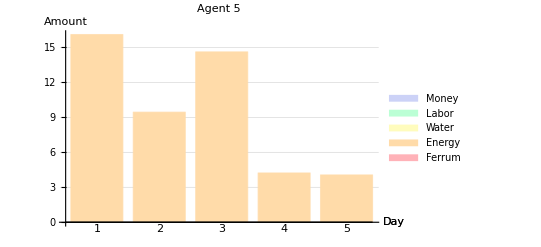
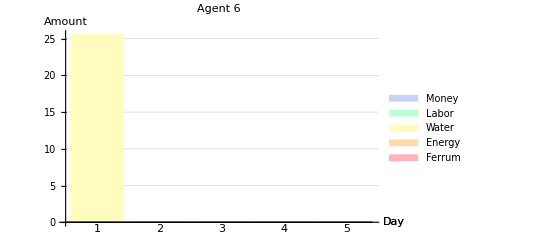
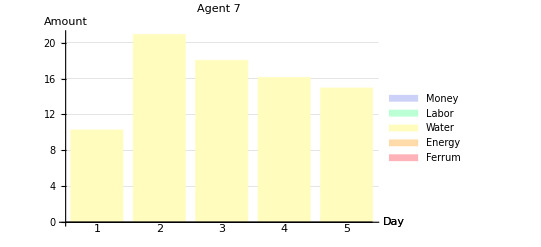
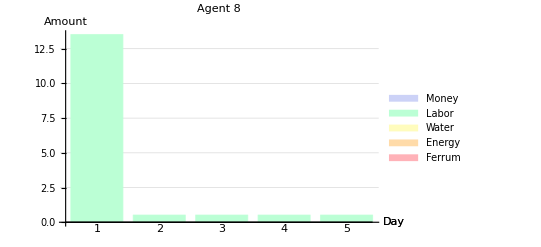

[an]: Shows all consumption of (an)-agent

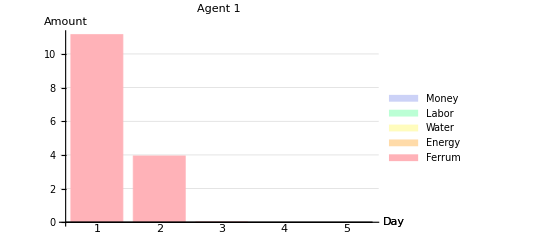
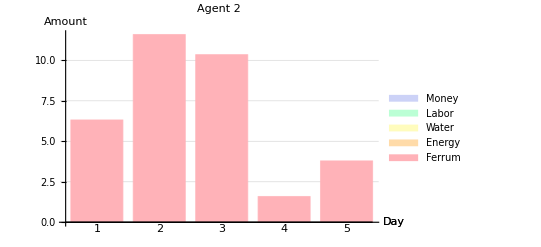
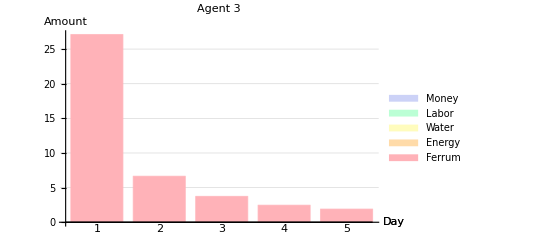
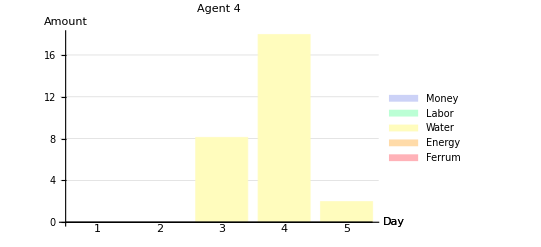
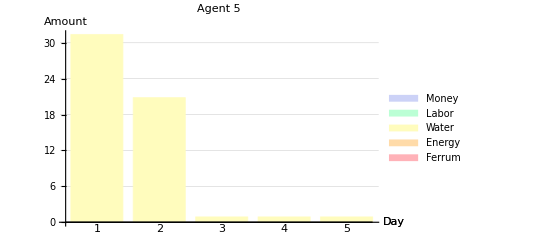
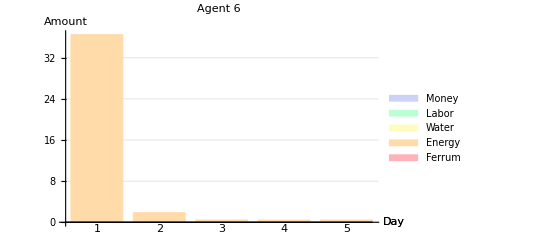
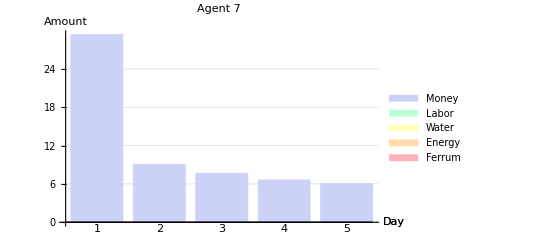
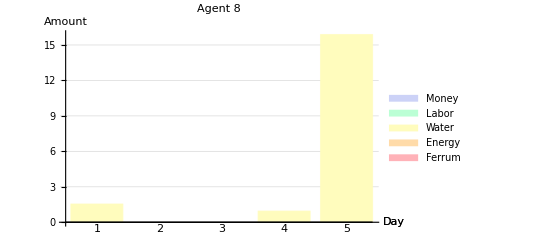

[an]: Shows how (an)-agent portfolio cost is changing

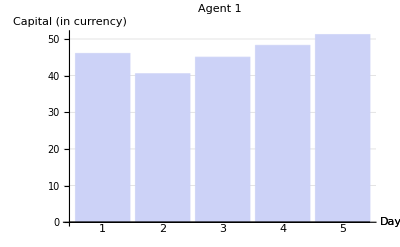
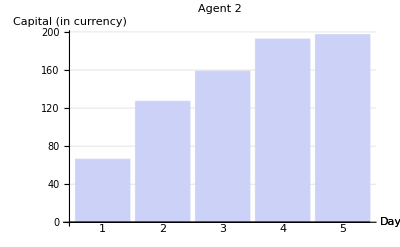
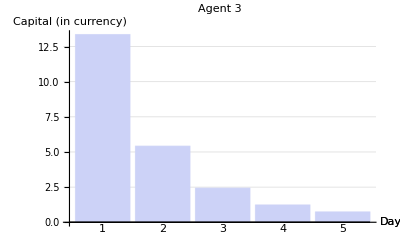
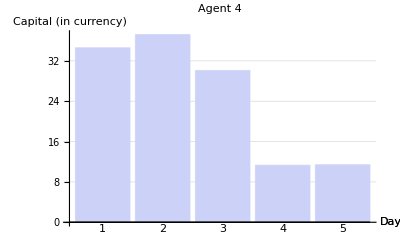
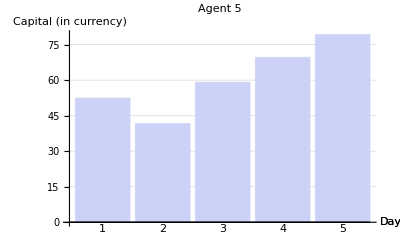
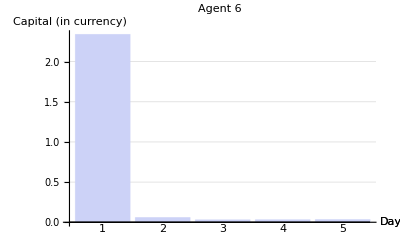
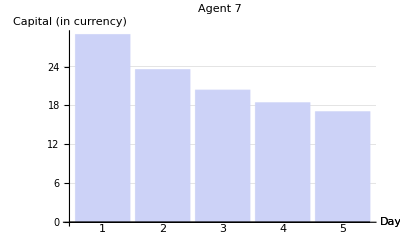
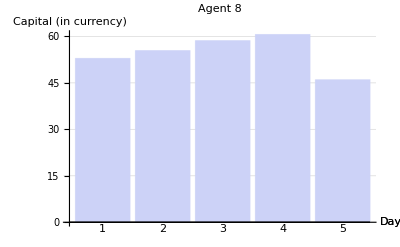

[pc]: Shows (pc)richest to (pc)poorest ratio

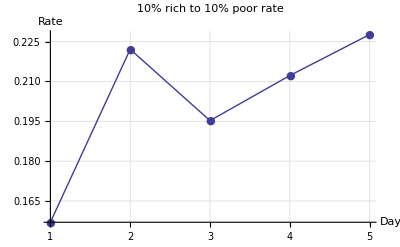

[bn]: Shows histogram of agents' richness with (bn) beans

[an]: Shows (an)-agent storage, claculated in it's main currency

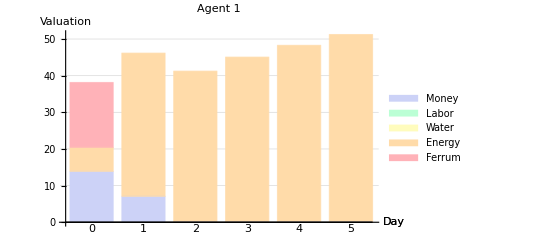
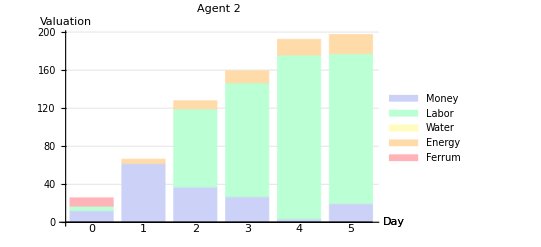
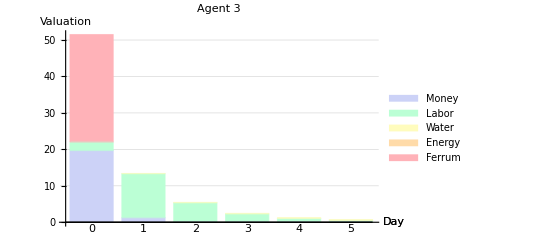
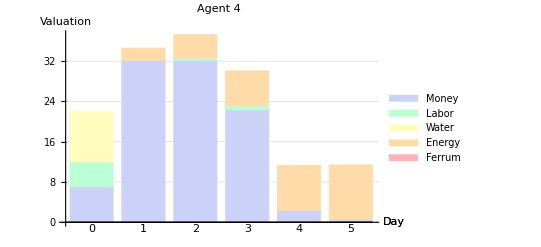
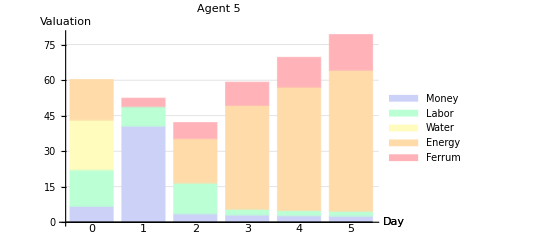
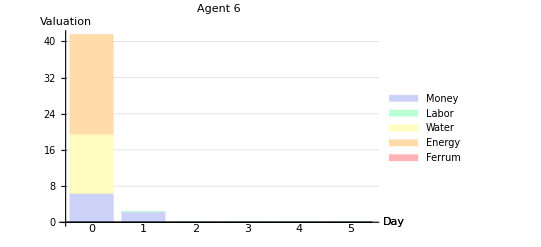
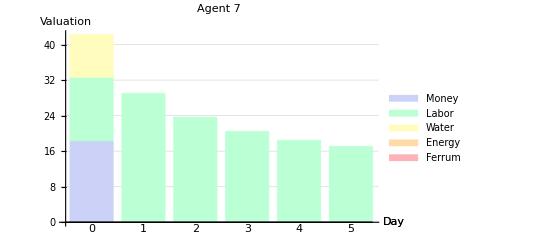
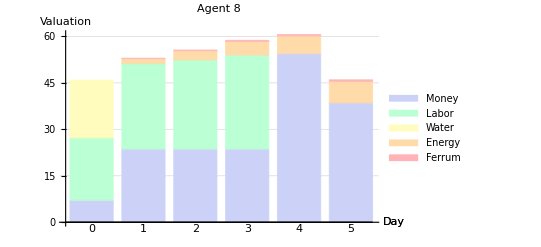

```mathematica
?MAEVisAgentCurrency
MAEVisAgentCurrency /@agentsNums

?MAEVisAgentProduce
MAEVisAgentProduce/@agentsNums

?MAEVisAgentConsume
MAEVisAgentConsume/@agentsNums

?MAEVisAgentCapital
MAEVisAgentCapital /@agentsNums

?MAEVisAgentsDifference
MAEVisAgentsDifference[10]

?MAEVisAgentsHistogram
MAEVisAgentsHistogram[10]

?MAEVisAgentProducts
MAEVisAgentProducts /@ agentsNums
```

```mathematica
?MAEVisAgentActionsTable
MAEVisAgentActionsTable /@ {1,2,3}
```

[an]: Table of all actions by (an)-agent

{DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 13.87 Money
4.15 Energy
9.42 Ferrum
1/1 | 19.09 Energy | m3: {Ask 26.16Ene x 1.74Mon}
m4: {Bid 7.34Fer x 1.88Mon, Bid 5.35Fer x 1.88Mon} | m4: [B]11.15Fer/20.98Mon | 11.15 Ferrum | 7.06 Money
23.64 Energy
1/2 |  | m3: {Ask 26.16Ene x 1.56Mon}
m4: {Bid 0.89Fer x 1.88Mon, Bid 0.65Fer x 1.88Mon} | m3: [S]2.53Ene/4.17Mon |  | 
2/1 | 0.16 Energy | m3: {Ask 26.73Ene x 1.54Mon}
m4: {Bid 2.17Fer x 1.88Mon, Bid 1.58Fer x 1.88Mon} | m4: [B]3.75Fer/6.71Mon | 3.94 Ferrum | 0.02 Money
26.73 Energy
2/2 |  | m3: {Ask 26.73Ene x 1.54Mon}
m4: {Bid 0.11Fer x 1.88Mon, Bid 0.08Fer x 1.88Mon} | m4: [B]0.19Fer/0.33Mon |  | 
3/1 | 0.16 Energy | m3: {Ask 29.81Ene x 1.50Mon}
m4: {Bid 0.01Fer x 1.85Mon, Bid 0.01Fer x 1.85Mon} | m4: [B]0.01Fer/0.02Mon | 0.01 Ferrum | 29.81 Energy
3/2 |  | m3: {Ask 29.81Ene x 1.50Mon}
m4: {Bid 0.00Fer x 1.85Mon} | m4: [B]0.00Fer/0.00Mon |  | 
4/1 | 0.16 Energy | m3: {Ask 32.90Ene x 1.46Mon} | --- | --- | 32.90 Energy
4/2 |  | m3: {Ask 32.90Ene x 1.46Mon} | --- |  | 
5/1 | 0.16 Energy | m3: {Ask 35.99Ene x 1.42Mon} | --- | --- | 35.99 Energy
5/2 |  | m3: {Ask 35.99Ene x 1.42Mon} | --- |  |  
Agent 1,DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 12.03 Money
4.65 Labor
4.73 Ferrum
1/1 | 53.53 Labor | m1: {Ask 60.33Lab x 1.02Mon} | m1: [S]52.95Lab/54.10Mon | 6.32 Ferrum | 61.62 Money
2.85 Energy
1/2 |  | m1: {Ask 7.39Lab x 0.19Mon}
m4: {Bid 22.45Fer x 2.07Mon} | m1: [S]7.39Lab/7.51Mon |  | 
2/1 | 139.46 Labor | m1: {Ask 141.61Lab x 0.92Mon} | m1: [S]23.91Lab/23.18Mon | 11.59 Ferrum | 36.83 Money
85.20 Labor
5.69 Energy
2/2 |  | m1: {Ask 117.70Lab x 0.90Mon}
m4: {Bid 10.00Fer x 1.99Mon} | m1: [S]32.49Lab/31.16Mon
m4: [B]10.00Fer/17.50Mon |  | 
3/1 | 85.66 Labor | m1: {Ask 173.01Lab x 0.90Mon} | m1: [S]20.68Lab/19.34Mon | 10.35 Ferrum | 26.67 Money
128.48 Labor
8.54 Energy
3/2 |  | m1: {Ask 152.33Lab x 0.88Mon}
m4: {Bid 8.76Fer x 1.90Mon} | m1: [S]23.85Lab/22.14Mon
m4: [B]8.76Fer/14.81Mon |  | 
4/1 | 63.60 Labor | m1: {Ask 194.23Lab x 0.87Mon} | --- | 1.59 Ferrum | 3.31 Money
190.57 Labor
11.38 Energy
4/2 |  | m1: {Ask 194.23Lab x 0.87Mon} | m1: [S]3.66Lab/3.31Mon |  | 
5/1 | 12.90 Labor | m1: {Ask 205.62Lab x 0.85Mon} | m1: [S]5.05Lab/4.44Mon | 3.79 Ferrum | 19.39 Money
179.61 Labor
14.23 Energy
5/2 |  | m1: {Ask 200.57Lab x 0.85Mon}
m4: {Bid 2.20Fer x 1.73Mon} | m1: [S]20.95Lab/18.39Mon
m4: [B]2.20Fer/3.43Mon |  |  
Agent 2,DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 19.67 Money
2.30 Labor
15.67 Ferrum
1/1 | 2.63 Money | m1: {Bid 11.21Lab x 1.02Mon}
m4: {Bid 10.15Fer x 2.07Mon} | m1: [B]11.21Lab/11.46Mon
m4: [B]10.15Fer/19.09Mon | 27.10 Ferrum | 1.24 Money
11.87 Labor
0.04 Water
1/2 |  | m1: {Bid 0.66Lab x 1.02Mon}
m4: {Bid 0.60Fer x 2.07Mon} | m1: [B]0.66Lab/0.67Mon |  | 
2/1 | 13.55 Money | m1: {Bid 5.17Lab x 1.02Mon}
m4: {Bid 5.05Fer x 1.91Mon} | m1: [B]5.17Lab/5.01Mon
m4: [B]5.05Fer/9.03Mon | 6.64 Ferrum | 0.07 Money
5.48 Labor
0.07 Water
2/2 |  | m1: {Bid 0.31Lab x 1.02Mon}
m4: {Bid 0.30Fer x 1.91Mon} | m1: [B]0.31Lab/0.30Mon
m4: [B]0.30Fer/0.53Mon |  | 
3/1 | 6.26 Money | m1: {Bid 2.35Lab x 0.97Mon}
m4: {Bid 2.34Fer x 1.79Mon} | m1: [B]2.35Lab/2.20Mon
m4: [B]2.34Fer/3.99Mon | 3.73 Ferrum | 0.02 Money
2.46 Labor
0.11 Water
3/2 |  | m1: {Bid 0.11Lab x 0.97Mon}
m4: {Bid 0.11Fer x 1.79Mon} | m1: [B]0.11Lab/0.10Mon
m4: [B]0.11Fer/0.18Mon |  | 
4/1 | 2.81 Money | m1: {Bid 1.12Lab x 0.94Mon}
m4: {Bid 1.12Fer x 1.71Mon} | m1: [B]1.12Lab/1.01Mon
m4: [B]1.12Fer/1.83Mon | 2.46 Ferrum | 0.01 Money
1.17 Labor
0.14 Water
4/2 |  | m1: {Bid 0.05Lab x 0.94Mon}
m4: {Bid 0.05Fer x 1.71Mon} | m1: [B]0.05Lab/0.05Mon
m4: [B]0.05Fer/0.08Mon |  | 
5/1 | 1.34 Money | m1: {Bid 0.58Lab x 0.91Mon}
m4: {Bid 0.59Fer x 1.64Mon} | m1: [B]0.58Lab/0.51Mon
m4: [B]0.59Fer/0.92Mon | 1.90 Ferrum | 0.00 Money
0.61 Labor
0.18 Water
5/2 |  | m1: {Bid 0.03Lab x 0.91Mon}
m4: {Bid 0.03Fer x 1.64Mon} | m1: [B]0.03Lab/0.02Mon
m4: [B]0.03Fer/0.04Mon |  |  
Agent 3}

## Goods

[pn]: Shows amount of producers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows amount of consumers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows daily production of (pn)-good

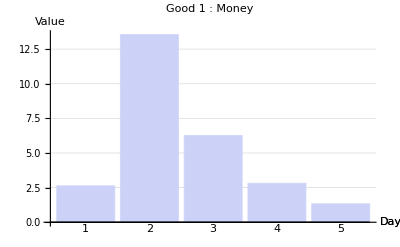
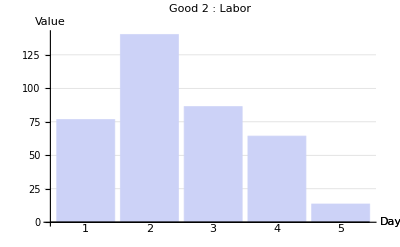
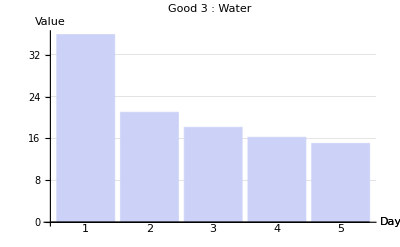
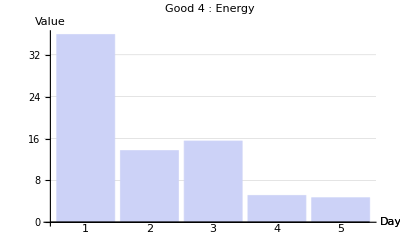
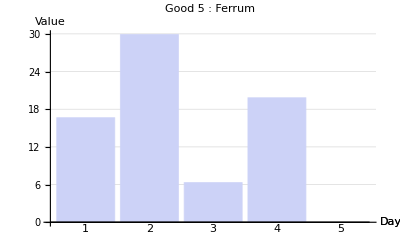

[pn]: Shows daily consumption of (pn)-good

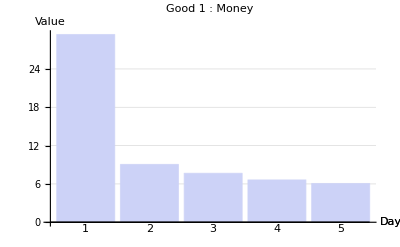
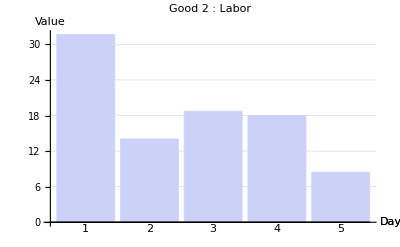
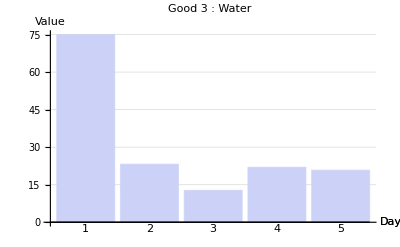
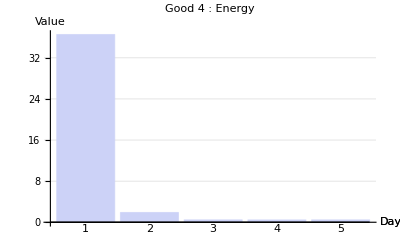
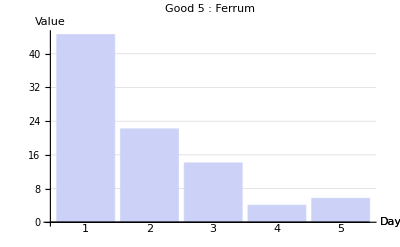

[pn]: Shows average production of (pn)-good (total prod a day / prod agents number)

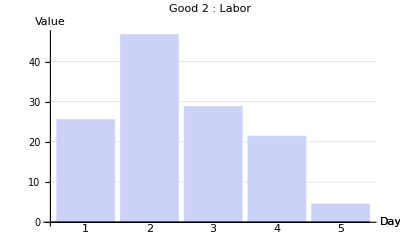
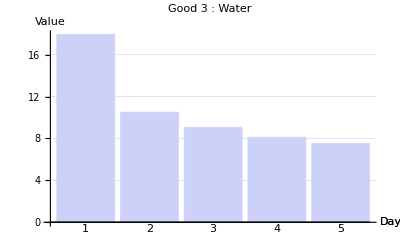
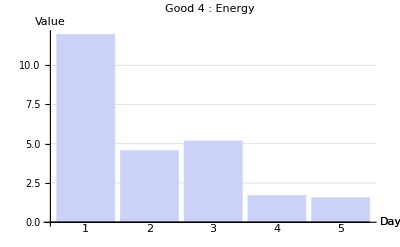
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows average consumption of (pn)-good (total cons a day / cons agents number)

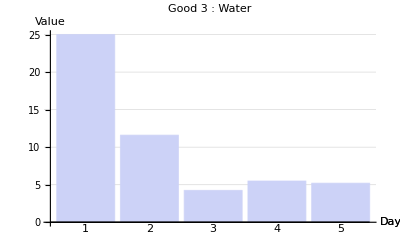
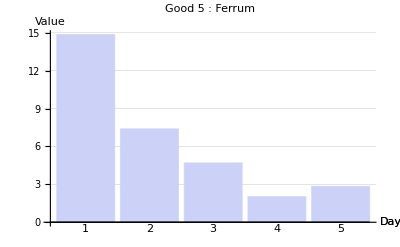
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows cumulative production of (pn)-good

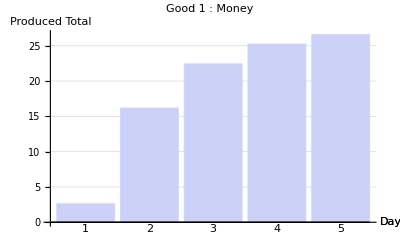
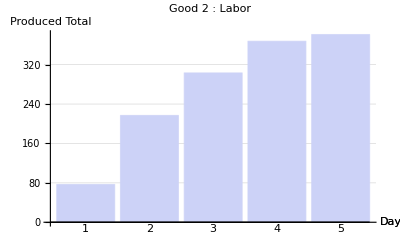
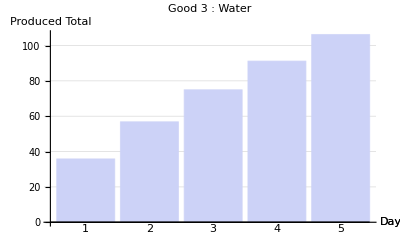
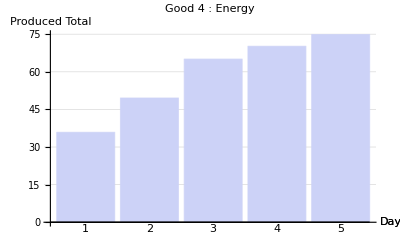
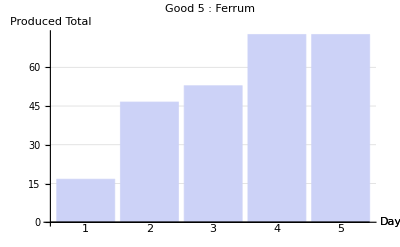

[pn]: Shows cumulative consumption of (pn)-good

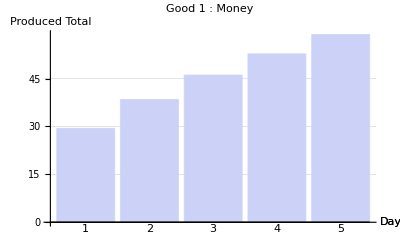
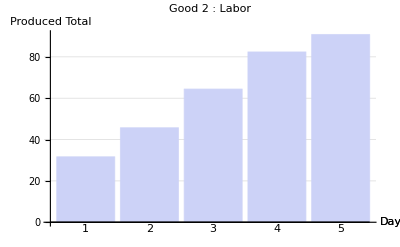
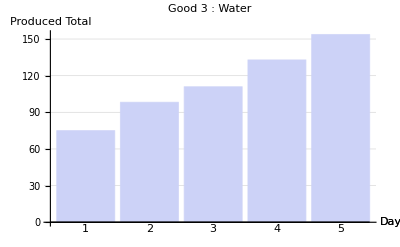
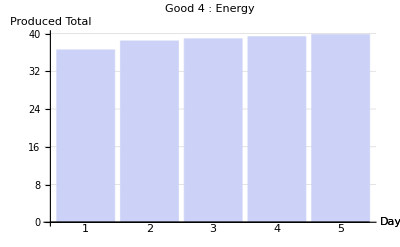
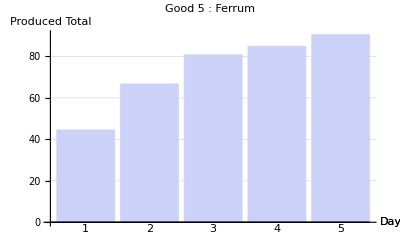

[pn]: Shows (pn)-good storage dynamics by agents

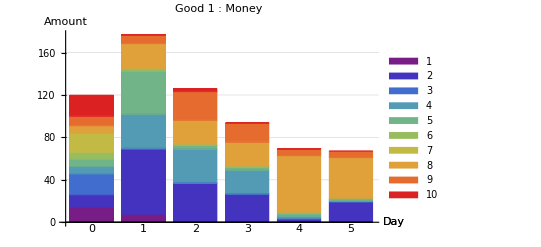
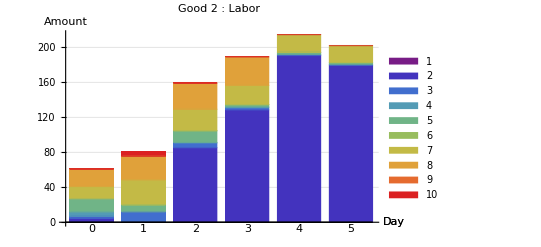
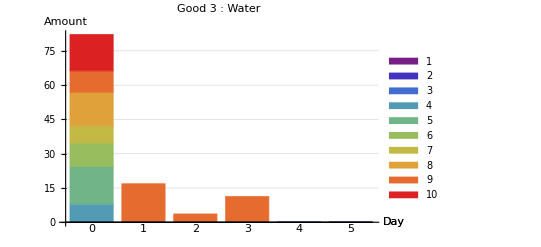
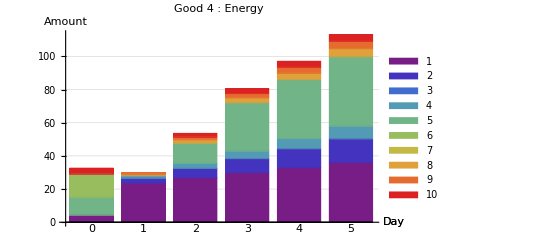
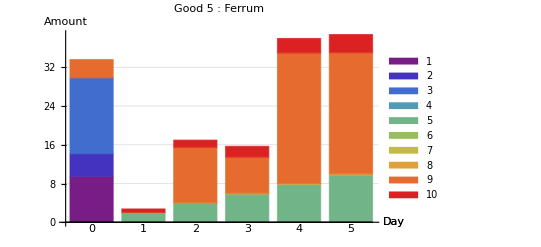

[pn]: Shows total (pn)-good storage dynamics

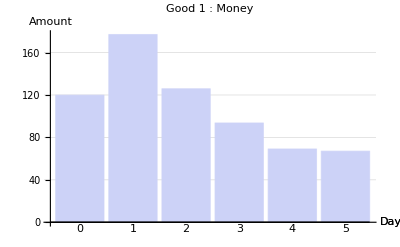
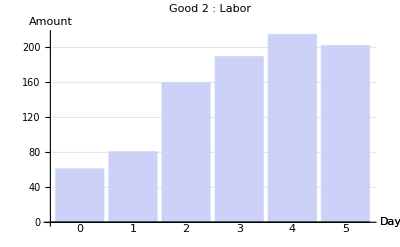
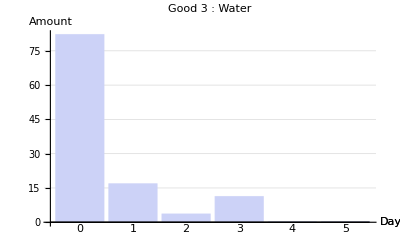
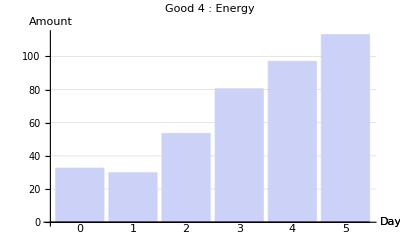
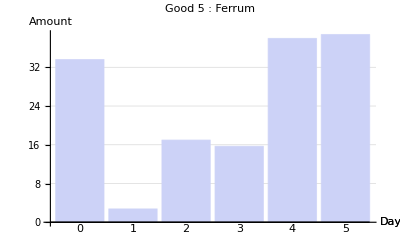

```mathematica
?MAEVisProducePart
MAEVisProducePart/@productsNums
?MAEVisConsumePart
MAEVisConsumePart/@productsNums

?MAEVisDailyProduce
MAEVisDailyProduce/@productsNums
?MAEVisDailyConsume
MAEVisDailyConsume/@productsNums

?MAEVisAverageProduce
MAEVisAverageProduce/@productsNums
?MAEVisAverageConsume
MAEVisAverageConsume/@productsNums

?MAEVisTotalProduction
MAEVisTotalProduction/@productsNums
?MAEVisTotalConsumption
MAEVisTotalConsumption/@productsNums

?MAEVisGoodStorage
MAEVisGoodStorage/@productsNums
?MAEVisTotalStorage
MAEVisTotalStorage/@ productsNums
```

## Markets

```mathematica
<<MultiAgent`
```

```mathematica
markets/@marketsNums //MatrixForm
```

(Title→Mon/Lab | G1→1 | G2→2 | SessionsInDay→2 | FirstPrice→{1,2}
Title→Mon/Wat | G1→1 | G2→3 | SessionsInDay→2 | FirstPrice→{1,2}
Title→Mon/Ene | G1→1 | G2→4 | SessionsInDay→2 | FirstPrice→{1,2}
Title→Mon/Fer | G1→1 | G2→5 | SessionsInDay→2 | FirstPrice→{1,2})

```mathematica
hMarketsBooks[[1,2,2]]
```

{{},{{2.81528,5.53319,Bid,2,69},{3.38358,5.86107,Bid,3,70},{1.62429,5.764,Bid,7,77},{1.81287,5.75746,Bid,8,80},{1.18098,5.5551,Bid,9,83}}}

[mn, dn, sn]: Shows (mn)-market book in the (dn)-day before (sn)-session start

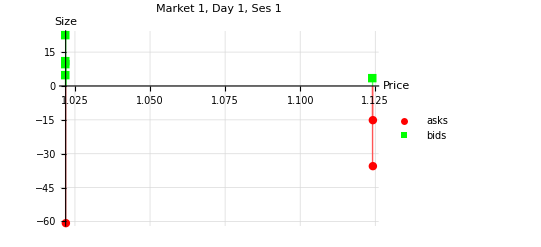

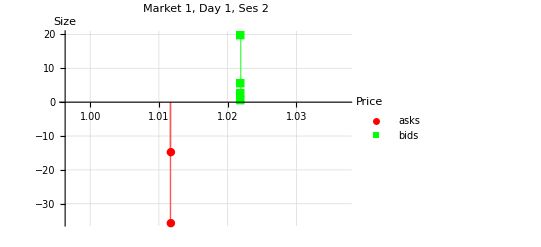
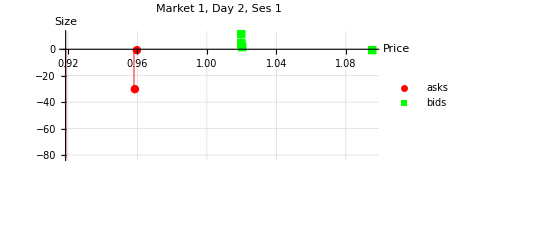
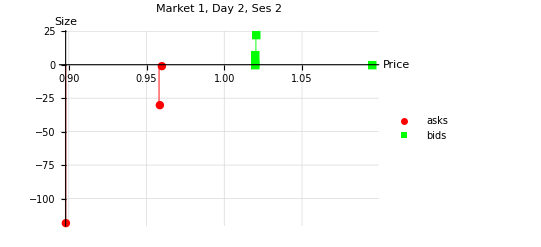
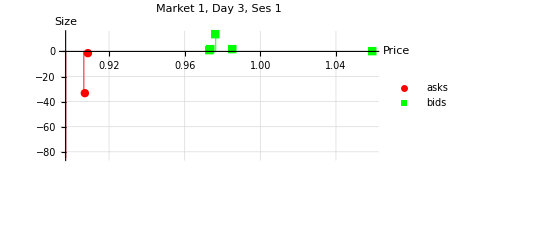
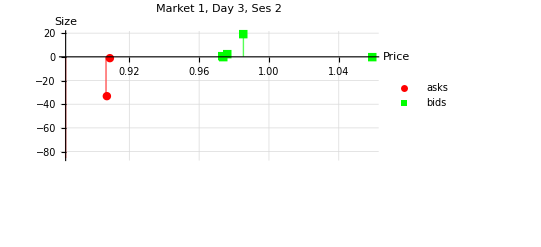
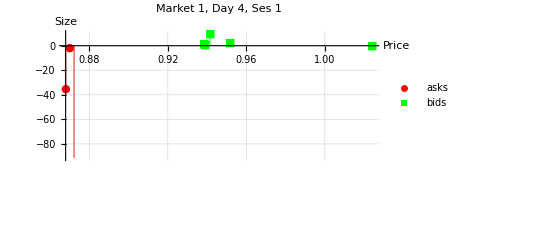
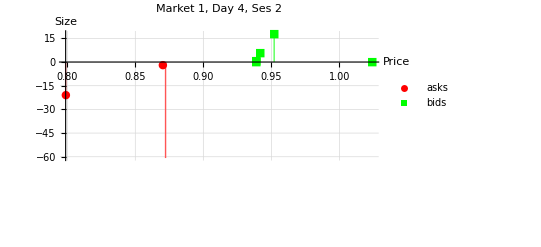
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?MAEVisMarketBook
mn = 1;
dn=1;
sn=1;
MAEVisMarketBook[mn, dn, sn]
MAEVisMarketBooksAll[mn]
```

[mn, dn, sn]: Shows double auction picture

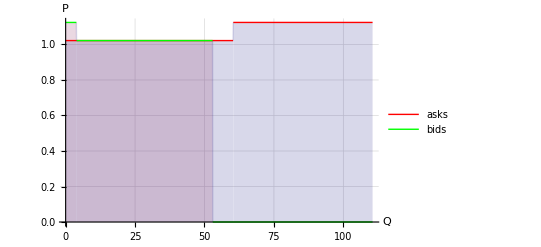

```mathematica
?MAEVisMarketAuction
mn = 1;
dn=1;
sn=1;
MAEVisMarketAuction[mn, dn, sn]
```

[an, mn] or [an, g1, g2]: Shows price dynamics with prognoses of [an]-agent

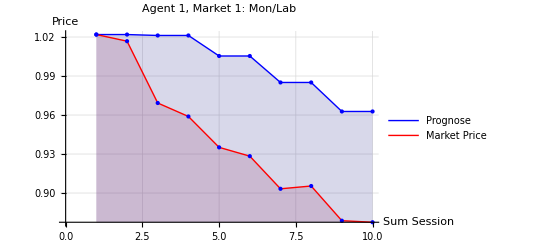

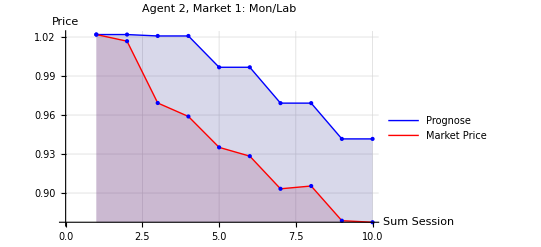
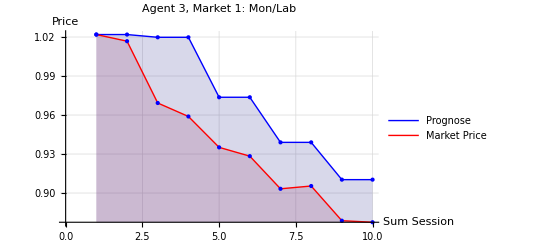
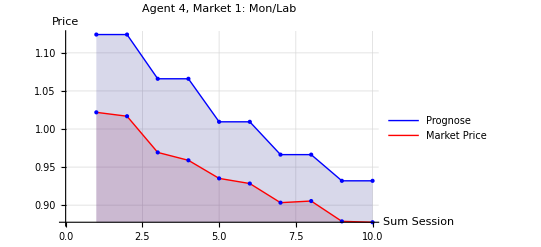
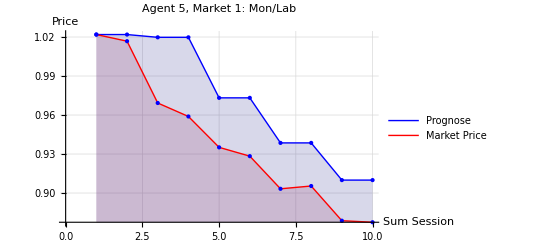
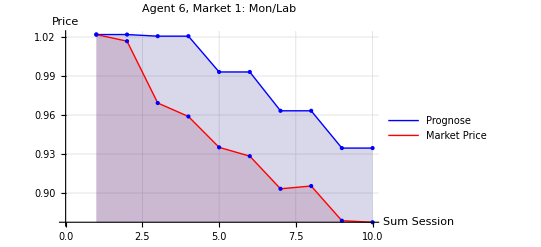
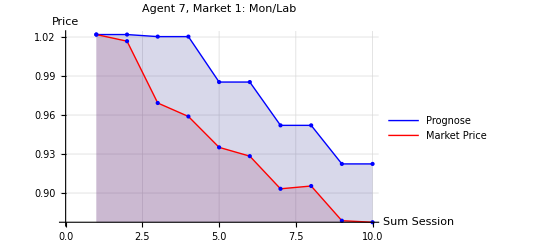
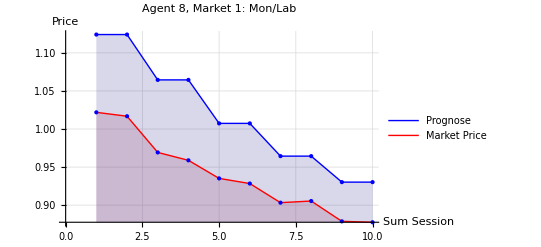
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?MAEVisPricePrognose
an=1;
mn = 1;
MAEVisPricePrognose[an, 1, 5];
MAEVisPricePrognose[an, mn]
MAEVisPricePrognose[#,mn ]&/@agentsNums
```

```mathematica
<<MultiAgent`
```

[mn]: Shows (mn)-market volume by day/session

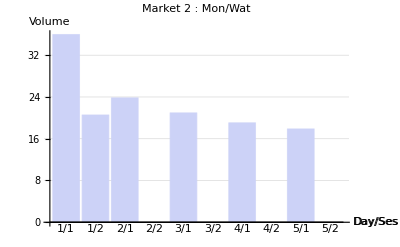

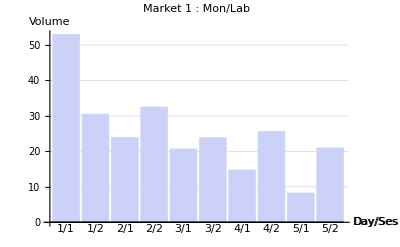
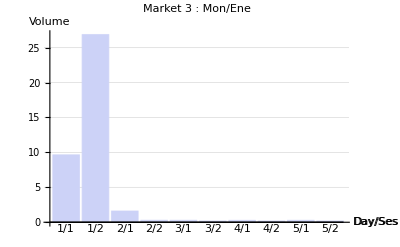
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[]: Shows total markets volume by day/session

-Graphics-

[mn]: Shows (mn)-market ask/bid orders amounts by day/session

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[]: Shows total ask/bid orders amounts by day/session

-Graphics-

[mn]: Shows (mn)-market deals amounts by day/session

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[]: Shows total orders amounts by day/session

-Graphics-

```mathematica
?MAEVisMarketVolume
MAEVisMarketVolume[2]
MAEVisMarketVolume /@ marketsNums

?MAEVisAllMarketVolume
MAEVisAllMarketVolume[]

?MAEVisMarketOrdersSize
MAEVisMarketOrdersSize[2]
MAEVisMarketOrdersSize /@ marketsNums

?MAEVisAllMarketOrdersSize
MAEVisAllMarketOrdersSize[]

?MAEVisMarketDealsSize
MAEVisMarketDealsSize[2]
MAEVisMarketDealsSize /@ marketsNums

?MAEVisAllMarketDealsSize
MAEVisAllMarketDealsSize[]
```

```mathematica
hMarketsDeals[[4,1,1]]
```

{{1,{-16.8012,2.63091}},{4,{16.8012,-2.63091}}}

```mathematica
?MAEVisMarketDealsTable
Column@(MAEVisMarketDealsTable /@ marketsNums)
```

[mn]: Table of deals on (mn)-market

DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | [S]52.95Lab/54.10Mon | [B]11.21Lab/11.46Mon | --- | [B]5.18Lab/5.29Mon | --- | [B]22.77Lab/23.27Mon | --- | [B]9.90Lab/10.11Mon | [B]3.89Lab/3.98Mon | 0
1/2 | --- | [S]7.39Lab/7.51Mon | [B]0.66Lab/0.67Mon | [S]14.74Lab/14.99Mon | [B]2.89Lab/2.94Mon | --- | [B]5.69Lab/5.79Mon | [S]8.35Lab/8.49Mon | [B]19.96Lab/20.29Mon | [B]1.29Lab/1.31Mon | 0
2/1 | --- | [S]23.91Lab/23.18Mon | [B]5.17Lab/5.01Mon | --- | [B]12.09Lab/11.72Mon | --- | [B]2.00Lab/1.94Mon | --- | [B]4.57Lab/4.43Mon | [B]0.07Lab/0.07Mon | 0
2/2 | --- | [S]32.49Lab/31.16Mon | [B]0.31Lab/0.30Mon | --- | [B]1.40Lab/1.34Mon | --- | [B]22.54Lab/21.61Mon | --- | [B]7.89Lab/7.57Mon | [B]0.34Lab/0.33Mon | 0
3/1 | --- | [S]20.68Lab/19.34Mon | [B]2.35Lab/2.20Mon | --- | [B]1.44Lab/1.34Mon | --- | [B]2.07Lab/1.94Mon | --- | [B]14.45Lab/13.51Mon | [B]0.37Lab/0.35Mon | 0
3/2 | --- | [S]23.85Lab/22.14Mon | [B]0.11Lab/0.10Mon | --- | [B]1.16Lab/1.07Mon | --- | [B]19.88Lab/18.45Mon | --- | [B]2.67Lab/2.48Mon | [B]0.04Lab/0.03Mon | 0
4/1 | --- | --- | [B]1.12Lab/1.01Mon | --- | [B]1.34Lab/1.21Mon | --- | [B]2.15Lab/1.94Mon | [S]14.75Lab/13.32Mon | [B]10.12Lab/9.14Mon | [B]0.03Lab/0.03Mon | 0
4/2 | --- | [S]3.66Lab/3.31Mon | [B]0.05Lab/0.05Mon | [S]1.37Lab/1.24Mon | [B]1.08Lab/0.98Mon | --- | [B]18.21Lab/16.49Mon | [S]20.58Lab/18.63Mon | [B]6.26Lab/5.67Mon | [B]0.00Lab/0.00Mon | 0
5/1 | --- | [S]5.05Lab/4.44Mon | [B]0.58Lab/0.51Mon | [S]0.46Lab/0.40Mon | [B]1.28Lab/1.13Mon | --- | [B]2.21Lab/1.95Mon | [S]2.74Lab/2.41Mon | [B]4.17Lab/3.66Mon | [B]0.00Lab/0.00Mon | 0
5/2 | --- | [S]20.95Lab/18.39Mon | [B]0.03Lab/0.02Mon | --- | [B]1.04Lab/0.92Mon | --- | [B]17.21Lab/15.10Mon | --- | [B]2.67Lab/2.35Mon | --- | 0 
Market 1: Mon/Lab
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | --- | --- | --- | [B]9.00Wat/11.49Mon | [S]35.96Wat/45.92Mon | --- | [B]1.54Wat/1.97Mon | [B]7.27Wat/9.29Mon | [B]18.14Wat/23.17Mon | 0
1/2 | --- | --- | --- | --- | [B]5.02Wat/6.70Mon | --- | [S]20.55Wat/27.42Mon | --- | [B]9.53Wat/12.72Mon | [B]5.99Wat/8.00Mon | 0
2/1 | --- | --- | --- | --- | [B]19.93Wat/25.22Mon | [S]0.21Wat/0.27Mon | [S]23.61Wat/29.88Mon | --- | [B]3.55Wat/4.49Mon | [B]0.35Wat/0.44Mon | 0
2/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
3/1 | --- | --- | --- | [B]8.11Wat/9.91Mon | --- | [S]0.21Wat/0.26Mon | [S]20.73Wat/25.33Mon | --- | [B]11.15Wat/13.62Mon | [B]1.69Wat/2.07Mon | 0
3/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
4/1 | --- | --- | --- | [B]17.95Wat/21.29Mon | --- | [S]0.21Wat/0.25Mon | [S]18.83Wat/22.33Mon | [B]0.95Wat/1.12Mon | --- | [B]0.15Wat/0.17Mon | 0
4/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
5/1 | --- | --- | --- | [B]1.98Wat/2.28Mon | --- | [S]0.21Wat/0.25Mon | [S]17.66Wat/20.38Mon | [B]15.88Wat/18.33Mon | --- | [B]0.01Wat/0.02Mon | 0
5/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0 
Market 2: Mon/Wat
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | --- | --- | --- | [S]5.34Ene/8.86Mon | [B]9.65Ene/16.01Mon | --- | --- | --- | [S]4.31Ene/7.15Mon | 0
1/2 | [S]2.53Ene/4.17Mon | --- | --- | --- | [S]24.35Ene/40.18Mon | [B]26.88Ene/44.34Mon | --- | --- | --- | --- | 0
2/1 | --- | --- | --- | --- | --- | [B]1.61Ene/2.53Mon | --- | --- | --- | [S]1.61Ene/2.53Mon | 0
2/2 | --- | --- | --- | --- | --- | [B]0.28Ene/0.43Mon | --- | --- | --- | [S]0.28Ene/0.43Mon | 0
3/1 | --- | --- | --- | --- | [S]0.28Ene/0.42Mon | [B]0.28Ene/0.42Mon | --- | --- | --- | --- | 0
3/2 | --- | --- | --- | --- | [S]0.18Ene/0.27Mon | [B]0.18Ene/0.27Mon | --- | --- | --- | --- | 0
4/1 | --- | --- | --- | --- | [S]0.27Ene/0.39Mon | [B]0.27Ene/0.39Mon | --- | --- | --- | --- | 0
4/2 | --- | --- | --- | --- | [S]0.18Ene/0.26Mon | [B]0.18Ene/0.26Mon | --- | --- | --- | --- | 0
5/1 | --- | --- | --- | --- | [S]0.27Ene/0.39Mon | [B]0.27Ene/0.39Mon | --- | --- | --- | --- | 0
5/2 | --- | --- | --- | --- | [S]0.18Ene/0.26Mon | [B]0.18Ene/0.26Mon | --- | --- | --- | --- | 0 
Market 3: Mon/Ene
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | [B]11.15Fer/20.98Mon | --- | [B]10.15Fer/19.09Mon | --- | --- | --- | --- | --- | [S]21.30Fer/40.07Mon | --- | 0
1/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
2/1 | [B]3.75Fer/6.71Mon | --- | [B]5.05Fer/9.03Mon | --- | --- | --- | --- | --- | [S]8.80Fer/15.74Mon | --- | 0
2/2 | [B]0.19Fer/0.33Mon | [B]10.00Fer/17.50Mon | [B]0.30Fer/0.53Mon | --- | --- | --- | --- | --- | [S]10.49Fer/18.36Mon | --- | 0
3/1 | [B]0.01Fer/0.02Mon | --- | [B]2.34Fer/3.99Mon | --- | --- | --- | --- | --- | [S]2.35Fer/4.01Mon | --- | 0
3/2 | [B]0.00Fer/0.00Mon | [B]8.76Fer/14.81Mon | [B]0.11Fer/0.18Mon | --- | --- | --- | --- | --- | [S]8.87Fer/15.00Mon | --- | 0
4/1 | --- | --- | [B]1.12Fer/1.83Mon | --- | --- | --- | --- | --- | [S]1.12Fer/1.83Mon | --- | 0
4/2 | --- | --- | [B]0.05Fer/0.08Mon | --- | --- | --- | --- | --- | [S]0.05Fer/0.08Mon | --- | 0
5/1 | --- | --- | [B]0.59Fer/0.92Mon | --- | --- | --- | --- | --- | [S]0.59Fer/0.92Mon | --- | 0
5/2 | --- | [B]2.20Fer/3.43Mon | [B]0.03Fer/0.04Mon | --- | --- | --- | --- | --- | [S]2.23Fer/3.47Mon | --- | 0 
Market 4: Mon/Fer

## Slide

```mathematica
<<MultiAgent`
```

```mathematica
?MAEVisAgentsHistogram
MAEVisAgentsHistogram[6]
```

[bn]: Shows histogram of agents' richness with (bn) beans